```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

# NV-Centre ESR Simulation

Construct a Hamiltonian of the form:

Ĥ =

Features to add:
- Enable truncated spin matrices
- Visualisation for the angular momentum conserving transitions
- Visualisation of the energies of the NV-center subsystem states
- Add Plot to RunSimulation function arguments
- Make RunSimulation add to a given list, instead of returning a list
- Make the freqStep dependent on the gradient of the curve. Instead of freqStep you could specify, number of datapoints per unit length on graph curve
- Function that returns a Rabi oscillation at a certain frequency
- Dephasing

## Initialisation

## Standard spin operators

```mathematica
(* Spin operators *)
Sx = 1/Sqrt[2]{ {  0, 1, 0} , { 1, 0, 1}, {0, 1, 0 } };
Sy = {{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}};
Sz = { {1, 0, 0 }, {0, 0, 0}, {0, 0, -1}};
eye = IdentityMatrix[3];

(* Electron triplet operators *)

eSx = KroneckerProduct[Sx, eye];
eSy = KroneckerProduct[Sy, eye];
eSz = KroneckerProduct[Sz, eye];

(* Nuclear operators *)

Ix = KroneckerProduct[eye, Sx];
Iy = KroneckerProduct[eye, Sy];
Iz = KroneckerProduct[eye, Sz];

(* Total angular momentum *)

Jx = eSx + Ix;
Jy = eSy + Iy;
Jz = eSz + Iz;
```

## Functions

#### GetFirstSubsystem[density, subSystemSize]

For a density matrix ρ in the space V = A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

Parameters:
- density [Matrix] - The density matrix is an n-by-n matrix, where n = dim(V).
- subSystemSize [Integer] - The dimension of A_1, dim(A_1).

```mathematica
GetFirstSubsystem[density_,subSystemSize_]:=Map[Tr,Partition[density,{Length[density]/subSystemSize,Length[density]/subSystemSize}],{2}];
```

#### FullHilbertSpaceOperator[operators, hilbertSubspaces]

Returns the matrix representation of an operator (Ô)_1⊗(Ô)_2⊗...⊗(Ô)_n.

Parameters:
- operators [List{ j [Integer] → op [Matrix], ...}] - A list of pairs. The second element of each pair is the matrix representation of the operator (Ô)_j, and the first element is the index j. Any unspecified operators for the subspaces will be replaced by an identity matrix of the appropriate size.
- hilbertSubspaces [List{Integer}] - A list of the dimensions of the subspaces j = 1, 2, ..., n.

Example:

Consider a system of two spin-1 particles, inhabiting Hilbert spaces V_1 and V_2 respectively, each of dimension 3. The total space is then V_1⊗ V_2. The following code will create the operator (Ŝ)_z⊗ (Ŝ)_z.

hilbertSubspaces = {3, 3};
Sz = SpinMatrixZ[1];
SzSz = FullHilbertSpaceOperator[ {1 → Sz, 2 → Sz }, hilbertSubspaces];

The variable operators should contain a list of pairs, where the second element is the operator acting on subsystem i, and where the first element is i. hilbertSubspaces is a list of the dimensions of the subspaces. Any unspecified operators for the subspaces will be replaced by an identity matrix of the appropriate size.

```mathematica
FullHilbertSpaceOperator[elem_ /; IntegerQ[elem[[1]]], hilbertSubspaces_] := FullHilbertSpaceOperator[{elem}, hilbertSubspaces];

FullHilbertSpaceOperator[ops_:{ elem_ /; IntegerQ[elem[[1]]] ..} , hilbertSubspaces_] := Module[
{operator = {1}, next},
Do[

next = Select[ ops, #[[1]] == i &];
next = If[next == {}, IdentityMatrix[hilbertSubspaces[[i]]], next[[1]][[2]]];
operator = KroneckerProduct[operator, next];
,{i, 1, Length[hilbertSubspaces]}];

operator
];
```

#### SpinMatrixX[spin]

Returns the spin matrix (Ŝ)_X, for a given spin.

Parameters:
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrixX[spin_] :=Table[
(i,j+1  + i+1,j)1/2 Sqrt[spin(spin+1) - i*j]
,{i, spin, -spin,-1},{j,spin, -spin, -1}]
```

#### SpinMatrixY[spin]

Returns the spin matrix (Ŝ)_Y, for a given spin.

Parameters:
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrixY[spin_] :=Table[
(i,j+1  - i+1,j)1/(2 I)Sqrt[spin(spin+1) - i*j]
,{i, spin, -spin, -1},{j, spin, -spin, -1}]
```

#### SpinMatrixZ[spin]

Returns the spin matrix (Ŝ)_Z, for a given spin.

Parameters:
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrixZ[spin_] :=Table[
i,j  j
,{i, spin, -spin, -1},{j, spin, -spin, -1}]
```

#### SpinMatrix[j, spin]

Returns the spin matrix (Ŝ)_j, for a given spin.

Parameters:
- j [Integer] - The axis of the projection.
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrix[j_/; Mod[j-1, 3] == 0, spin_] := SpinMatrixX[spin];
SpinMatrix[j_/; Mod[j-1, 3] == 1, spin_] := SpinMatrixY[spin];
SpinMatrix[j_/; Mod[j-1, 3] == 2, spin_] := SpinMatrixZ[spin];
```

#### SpinSpinHamiltonian[spins, couplings]

Returns a Hamiltonian of the form ∑_ij (k_(ij,x) (Ŝ)_(i,x)(Ŝ)_(j,x) + k_(ij,y) (Ŝ)_(i,y)(Ŝ)_(j,y) + k_(ij,z) (Ŝ)_(i,z)(Ŝ)_(j,z)), representing n interacting spins.

Parameters:

spins [List{Rational}] - An ordered list of spins {spin1, spin2, ...} in the system.
couplings [List{ { i [Integer] → j [Integer], coupling [Float or 3-vector] }, ... }] - List of elements of the form {subsystemIndexOfSpin1 → subsystemIndexOfSpin2, coupling}. coupling could either be a single Floating point constant, for an isotropic spin-spin coupling, or a 3-vector {A_x, A_y, A_z} for an anisotropic coupling.

Example:

We have three interacting spin-1/2 particles labelled i = 1, 2, 3. The interactions 1 ↔ 2 and 1 ↔ 3 are isotropic, but 2 ↔ 3 is anisotropic. Particle 1 has a zero-field-splitting D. The following code creates the Hamiltonian of the system.

ℋspinSpin =  SpinSpinHamiltonian[
   spins,
   {{1 → 1, {0, 0, D}},
    {1 → 2, k12},
    {1 → 3, k13},
    {2 → 3, {k23x, k23y, k23z}}}
] ;

```mathematica
SpinSpinHamiltonian[spins_, couplings_ : { { _ -> _,  _} ..}] := Module[
{H, spin1, spin2, sx, sy,sz, i, j, coeffs},

H = ConstantArray[0, {Times @@ (2spins + 1),Times @@ (2spins + 1)}];

Do[
i = c[[1]][[1]] ;
j = c[[1]][[2]] ;
coeffs = {};

Which[
NumberQ[c[[2]]],
coeffs = {c[[2]], c[[2]], c[[2]]},
Length[c[[2]]] == 3,
coeffs = c[[2]]
];

H = H + Sum[
coeffs[[k]]*FullHilbertSpaceOperator[ 
i->  SpinMatrix[k, spins[[i]]],
2*spins+1
] .FullHilbertSpaceOperator[ 
j ->  SpinMatrix[k, spins[[j]]],
2*spins+1
]
,{k, 1, 3}];

,{c, couplings}];
H
];
```

#### ZeemanHamiltonian[spins, ωs]

Returns a Zeeman Hamiltonian for the specified spins, of the form ∑_i ω_i(Ŝ)_(i,z).

Parameters:

- spins [List{Rational}] - An ordered list of spins {spin1, spin2, ...} for each particle.
- ωs [List{Float}] - An ordered list of Zeeman constants corresponding to each spin.

```mathematica
ZeemanHamiltonian[spins_, ωs_] :=Sum[
ωs[[i]]*FullHilbertSpaceOperator[i ->  SpinMatrixZ[spins[[i]]], 2spins+1]
,{i, 1, Length[spins]}]
```

#### NVCenterEnergySpectrum[ℋ, spins]

s

```mathematica
NVCenterEnergySpectrum[ℋ_, spins_] := Module[
{basis, mult = 2spins + 1, eig, energies, states,vecDecomps , vecsIndices, vecs, strs,
coeff, label,Jz, angMoms, table, data },
basis[indices_]:= Apply[KroneckerProduct, Table[
RotateRight[Flatten[IdentityMatrix[{1,mult[[i]]}]], indices[[i]]  - 1]
,{i, 1, Length[spins]}]] // Flatten;

eig = Eigensystem[ℋ];
energies = eig[[1]];
states = eig[[2]];

vecDecomps = {};
Do[
vecsIndices = Tuples[Map[Range, mult]];
vecs = Map[ basis, vecsIndices];
strs = {};
Do[
coeff = Conjugate[vecs[[i]]] . states[[k]];
label = Style["|"<>StringRiffle[Table[ (spins[[j]]-vecsIndices[[i]][[j]] + 1)//Rationalize, {j, 1, Length[spins]}],","]<>"⟩", Bold];

If[ coeff ≠ 0, AppendTo[strs,coeff * label]];
,{i, 1, Length[vecsIndices]}];

AppendTo[vecDecomps, strs];
,{k, 1, Length[states]}];

Jz = FullHilbertSpaceOperator[{1 -> SpinMatrixZ[spins[[1]] ]}  , mult] +
FullHilbertSpaceOperator[{2 -> SpinMatrixZ[spins[[2]] ]}  ,mult];
angMoms = Map[ # . Jz . # &, states];

data = {
energies,
vecDecomps,
states,
angMoms
};

data = Sort[Transpose[data], #1[[1]] > #2[[1]] &] // Transpose; 

table = {
Prepend[Prepend[data[[1]], "---"], Style["E", Bold]],
Prepend[ Prepend[data[[2]], "---"], Style["|ψ_E⟩", Bold]],
Prepend[Prepend[data[[4]], "---"],  Style["⟨J_z⟩", Bold]]
} // Transpose //MatrixForm;
{data, table}
];
```

#### NVCenterEnergySpectrum2[ℋ, spins]

s

```mathematica
NVCenterEnergySpectrum2[ℋ_, spins_] := Module[
{basis, mult = 2spins + 1, eig, energies, states,vecDecomps , vecsIndices, vecs, strs,
coeff, label,Jz, angMoms, table, data },
basis[indices_]:= Apply[KroneckerProduct, Table[
RotateRight[Flatten[IdentityMatrix[{1,mult[[i]]}]], indices[[i]]  - 1]
,{i, 1, Length[spins]}]] // Flatten;

states = IdentityMatrix[Length[ℋ]];
energies = Table[Conjugate[s] .ℋ . s,{s, states}];

vecDecomps = {};
Do[
vecsIndices = Tuples[Map[Range, mult]];
vecs = Map[ basis, vecsIndices];
strs = {};
Do[
coeff = Conjugate[vecs[[i]]] . states[[k]];
label = Style["|"<>StringRiffle[Table[ (spins[[j]]-vecsIndices[[i]][[j]] + 1)//Rationalize, {j, 1, Length[spins]}],","]<>"⟩", Bold];

If[ coeff ≠ 0, AppendTo[strs,coeff * label]];
,{i, 1, Length[vecsIndices]}];

AppendTo[vecDecomps, strs[[1]]];
,{k, 1, Length[states]}];

Jz = FullHilbertSpaceOperator[{1 -> SpinMatrixZ[spins[[1]] ]}  , mult] +
FullHilbertSpaceOperator[{2 -> SpinMatrixZ[spins[[2]] ]}  ,mult];
angMoms = Map[ # . Jz . # &, states];

data = {
energies,
vecDecomps,
states,
angMoms
};

data = Sort[Transpose[data], #1[[1]] > #2[[1]] &] // Transpose; 

table = {
Prepend[Prepend[data[[1]], "---"], Style["E", Bold]],
Prepend[ Prepend[data[[2]], "---"], Style["|ψ_E⟩", Bold]],
Prepend[Prepend[data[[4]], "---"],  Style["⟨J_z⟩", Bold]]
} // Transpose //MatrixForm;
{data, table}
];
```

#### GetSybsystemA[density, subSystemSize]

For a density matrix ρ in the space A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

```mathematica
GetFirstSubsystem[density_, subSystemSize_] := Map[ Tr, Partition[ density, {Length[density]/subSystemSize, Length[density]/subSystemSize}], {2}];
```

#### RunSimulation[freqStart, freqEnd, freqStep, ℋ, spins, spinVec, density0]

sd

```mathematica
RunSimulation[freqStart_, freqEnd_, freqStep_, tStart_, tEnd_, ℋ_, spins_, stateVecs_, density0_] := Module[
{calculations,systemSize, density, eqnTotal, eqns, diffeqs, funcs, initialStateEqs, params, subsystem,
data, tic, count, sol, pulseFreq, pFunc, p, prw, toc, ttot,
totalj, sj, ij, Jz, Sz, Iz, simData},
calculations = Table[f, {f, freqStart, freqEnd, freqStep}] // Length;

(* Setup Density matrix *)
systemSize = Apply[Times, 2spins+1];
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

(* Define master equation *)

eqnTotal = ⅈ  D[ density, t] - (ℋ[f, t].density - density.ℋ[f, t]) // Simplify;

eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;

(* Perform simulation *)

data = Table[ {}, {i, 1, Length[stateVecs]}]; (* Store spinVec probability data for each frequency *)
tic=AbsoluteTime[];
count = 1;

(*plot =Dynamic[ListPlot[data], TrackedSymbols:>{data}];
Print[plot];*)

(* Angular momentum *)

totalj = {};
sj = {};
ij = {};

Sz = FullHilbertSpaceOperator[{1 -> SpinMatrixZ[spins[[1]] ]}  , {3, 3}];
Iz = FullHilbertSpaceOperator[{2 -> SpinMatrixZ[spins[[2]] ]}  , {3, 3}];
Jz =Sz + Iz;

Do[
sol = NDSolve[ params /. f -> freq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->7,AccuracyGoal->7, MaxSteps->Infinity];

Do[
pFunc = Conjugate[stateVecs[[i]]] .density. stateVecs[[i]];
p = 1/(tEnd - tStart)NIntegrate[pFunc /. sol, {t, tStart, tEnd}];
AppendTo[data[[i]], {freq, p[[1]]}];
, {i, 1, Length[stateVecs]}];

p = 1/(tEnd - tStart)NIntegrate[ Tr[ density . Jz] /. sol, {t, tStart, tEnd}];
AppendTo[totalj, {freq, p[[1]] }];
p = 1/(tEnd - tStart)NIntegrate[ Tr[ density . Sz] /. sol, {t, tStart, tEnd}];
AppendTo[sj, {freq, p[[1]] }];
p = 1/(tEnd - tStart)NIntegrate[ Tr[ density . Iz] /. sol, {t, tStart, tEnd}];
AppendTo[ij, {freq, p[[1]] }];

NotebookDelete[prw];
prw = PrintTemporary["Calculation ", count, " out of ", calculations];
count = count + 1;

, {freq, freqStart, freqEnd, freqStep}];

toc=AbsoluteTime[];
ttot = N[(toc-tic)/60];
Print["Total time taken (min) = ",ttot];


(* Prepare and refactor data *)

(* Extract the data into variables with appropriate names *)
(* simData[1, -1] contains the simulation results for the |1,-1⟩ state for example *)
Do[
simData[1- ( (i- 1)/3 // Floor), 1- Mod[i-1, 3]] = data[[ i ]];
,{i, 1, 9}];

simData["allstates"] = data;
simData["Jz"] = totalj;
simData["Sz"] =sj;
simData["Iz"] = ij;

simData["totalSimulationTime"] = ttot;

simData["T(1)"]= Table[ {simData["allstates"][[1]][[i]][[1]],  simData["allstates"][[1]][[i]][[2]] + simData["allstates"][[2]][[i]][[2]] + simData["allstates"][[3]][[i]][[2]]},  {i, 1, Length[simData["allstates"][[1]]]}];
simData["T(0)"]= Table[ {simData["allstates"][[1]][[i]][[1]],  simData["allstates"][[4]][[i]][[2]] + simData["allstates"][[5]][[i]][[2]] + simData["allstates"][[6]][[i]][[2]]},  {i, 1, Length[simData["allstates"][[1]]]}];
simData["T(-1)"]= Table[ {simData["allstates"][[1]][[i]][[1]],  simData["allstates"][[7]][[i]][[2]] + simData["allstates"][[8]][[i]][[2]] + simData["allstates"][[9]][[i]][[2]]},  {i, 1, Length[simData["allstates"][[1]]]}];

simData

];
```

#### SolveSystem[tStart, tEnd, ℋ, freq, density0]

sdsd

```mathematica
SolveSystem[tStart_, tEnd_, ℋ_,freq_, density0_ ] := Module[
{systemSize, density, eqnTotal, eqns, diffeqs, funcs, initialStateEqs, params},
(* Setup Density matrix *)
systemSize = Length[density0];
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

(* Define master equation *)

eqnTotal = ⅈ  D[ density, t] - (ℋ[f, t].density - density.ℋ[f, t]) // Simplify;

eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;

{density, NDSolve[ params /. f -> freq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->7,AccuracyGoal->7, MaxSteps->Infinity]}
];
```

#### LoadSimulationData[dir]

When running the simulation, data is exported into separate folders. This function will load simulation data from a specific run, given the folder directory path. The path could either be the full path, or a relative path from the current notebook directory.

The function will return a variable that contains the data. The data is stored in the following DownValues:

simData=LoadSimulationData[dir]
simData[i,j] (*with i,j=1,0,-1,for the states|1,1⟩|1,0⟩|1,-1⟩|0,1⟩|0,0⟩|0,-1⟩|-1,1⟩|-1,0⟩|-1,-1⟩) *)
simData[“allstates”] (* Contains the data for all the states in canonical order *)
simData[“Jz”] (* Total angular momentum *)
simData[“Sz”] (* Electron triplet spin angular ngular momentum *)
simData[“Iz”] (* Nuclear spin angular momentum *)

```mathematica
LoadSimulationData[dir_] := Module[
{simData, ms, mi, stateStr, pre},

simData["allstates"] = {};
pre = FileNameSplit[dir]//Last;

Do[
ms = 1- ( (i- 1)/3 // Floor);
mi = 1- Mod[i-1, 3];
stateStr = "state(" <> ToString[ms] <> "," <> ToString[mi] <>")";
simData[ms, mi] = Import[FileNameJoin[{ dir, pre<>"_data_"<> stateStr <> ".csv" }]];
AppendTo[simData["allstates"], simData[ms, mi]];
,{i, 1, 9}];

simData["T(1)"] =  Import[ FileNameJoin[{dir, pre <> "_data_T(1).csv"}]];
simData["T(0)"] =  Import[ FileNameJoin[{dir, pre <> "_data_T(0).csv"}]];
simData["T(-1)"] =  Import[ FileNameJoin[{dir, pre <> "_data_T(-1).csv"}]];

simData["Jz"] = Import[ FileNameJoin[{dir, pre <> "_data_Jz.csv"}]];
simData["Iz"] =Import[ FileNameJoin[{dir, pre <> "_data_Iz.csv"}]];
simData["Sz"] = Import[ FileNameJoin[{dir, pre <> "_data_Sz.csv"}]];

simData
]
```

# No spin-bath

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

#### Simulation parameters

```mathematica
pulseAmplitude = 1*10^6; (* [Hz] *)
pulseAmplitudeE = pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 3.12*^9; (* [Hz] *)
pulseFreqEnd =3.18*^9; (* [Hz] *) 
pulseFreqStep = 0.1*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 601

#### Setup Hamiltonian

```mathematica
spins = {1, 1};
hilbertSubspaceDimensions = 2*spins + 1;

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋspinSpin =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋspinSpin + ℋzee;

ℋCop =  (pulseAmplitudeE* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1] }, hilbertSubspaceDimensions ]  + pulseAmplitudeN * FullHilbertSpaceOperator[ { 2-> SpinMatrixX[1] }, hilbertSubspaceDimensions ] );

ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

```mathematica
op = KroneckerProduct[Sx, IdentityMatrix[3]];
op = KroneckerProduct[Sx, IdentityMatrix[3]] + KroneckerProduct[IdentityMatrix[3], Sx];
op = ℋCop;

pairs = Select [Flatten[Table[ {i,j}, {i, 1,9}, {j , 1, 9}], 1], op[[ #[[1]], #[[2]] ]] ≠ 0 &];

iToVec[i_] := "|" <> ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[ 1- Mod[i-1, 3]] <> "⟩";

Map[ iToVec[#[[1]]] ↔ iToVec[#[[2]]] &, pairs] // MatrixForm
```

(|1,1⟩↔|1,0⟩
|1,1⟩↔|0,1⟩
|1,0⟩↔|1,1⟩
|1,0⟩↔|1,-1⟩
|1,0⟩↔|0,0⟩
|1,-1⟩↔|1,0⟩
|1,-1⟩↔|0,-1⟩
|0,1⟩↔|1,1⟩
|0,1⟩↔|0,0⟩
|0,1⟩↔|-1,1⟩
|0,0⟩↔|1,0⟩
|0,0⟩↔|0,1⟩
|0,0⟩↔|0,-1⟩
|0,0⟩↔|-1,0⟩
|0,-1⟩↔|1,-1⟩
|0,-1⟩↔|0,0⟩
|0,-1⟩↔|-1,-1⟩
|-1,1⟩↔|0,1⟩
|-1,1⟩↔|-1,0⟩
|-1,0⟩↔|0,0⟩
|-1,0⟩↔|-1,1⟩
|-1,0⟩↔|-1,-1⟩
|-1,-1⟩↔|0,-1⟩
|-1,-1⟩↔|-1,0⟩)

#### Energy spectrum of the unperturbed Hamiltonian

In terms of the eigenstates of the Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV, spins]; 
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

```mathematica
hamiltonianSpectrum[[1]][[1]]
```

{3.15026×10^9,3.1475×10^9,3.14312×10^9,2.58975×10^9,2.58692×10^9,2.58266×10^9,-3105.84,-4.92093×10^6,-4.98216×10^6}

```mathematica
{3.1502573369663377*^9,3.1474981066489053*^9,3.1431151730484695*^9,2.5897457603508644*^9,2.586924999188904*^9,2.5826648269515305*^9,-3105.8378033638,-4.920933399331093*^6,-4.9821639178676605*^6} - 
{3.1474981066489053*^9,3.1431151730484695*^9,2.5897457603508644*^9,2.586924999188904*^9,2.5826648269515305*^9,-3105.8378033638,-4.920933399331093*^6,-4.9821639178676605*^6, 0}
```

{2.75923×10^6,4.38293×10^6,5.53369×10^8,2.82076×10^6,4.26017×10^6,2.58267×10^9,4.91783×10^6,61230.5,-4.98216×10^6}

In terms of eigenstates of the spin triplet and nuclear spin

```mathematica
hamiltonianSpectrumPure = NVCenterEnergySpectrum2[ℋ[0,0], spins];
hamiltonianSpectrumPure[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | |-1,0⟩ | -1
3.1475×10^9 | |-1,1⟩ | 0
3.14312×10^9 | |-1,-1⟩ | -2
2.58974×10^9 | |1,0⟩ | 1
2.58692×10^9 | |1,-1⟩ | 0
2.58266×10^9 | |1,1⟩ | 2
0. | |0,0⟩ | 0
-4.91923×10^6 | |0,1⟩ | 1
-4.98077×10^6 | |0,-1⟩ | -1)

```mathematica
4.980766242049094*^6 + 3.1502559392905188*^9
```

3.15524×10^9

#### Initial state

```mathematica
eig = Eigensystem[ℋNV];

eigenStates[0,1] = hamiltonianSpectrum[[1]][[3]][[8]];
eigenStates[0,0] = hamiltonianSpectrum[[1]][[3]][[7]];
eigenStates[0,-1] = hamiltonianSpectrum[[1]][[3]][[9]];
```

```mathematica
initialState = IdentityMatrix[9][[4]] (* 0,1 *)
initialState = IdentityMatrix[9][[5]] (* 0,0 *)
initialState = IdentityMatrix[9][[6]] (* 0,-1 *)

density0 = Outer[Times, initialState, initialState];
```

{0,0,0,1,0,0,0,0,0}

{0,0,0,0,1,0,0,0,0}

{0,0,0,0,0,1,0,0,0}

```mathematica
density0 = 1/3(Outer[Times,  IdentityMatrix[9][[4]],  IdentityMatrix[9][[4]]] + Outer[Times,  IdentityMatrix[9][[5]],  IdentityMatrix[9][[5]]] +Outer[Times,  IdentityMatrix[9][[6]],  IdentityMatrix[9][[6]]]);
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Rabi Oscillations

```mathematica
res = SolveSystem[ tStart, tEnd/5, ℋ,3.155236705532568*^9, density0];
rho =res[[1]];
funcs = Table[ v . rho . v, {v, IdentityMatrix[9]}] /. res[[2]][[1]];

tf[1] = Total[funcs[[1;;3]]];
tf[0] = Total[funcs[[4;;6]]];
tf[-1] = Total[funcs[[7;;9]]];
```

-5.54769×10^6+1.21908×10^-8 ⅈ

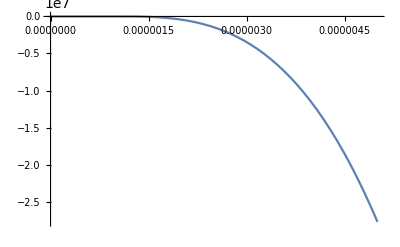

```mathematica
NIntegrate[ tf[0], {t, tStart, tEnd}] 1/tEnd

Plot[tf[0], {t, tStart,tEnd}, PlotRange->{Full, Full}]
```

```mathematica
Table[ {i,NIntegrate[funcs[[i]], {t, tStart, tEnd}] 1/tEnd }, {i, 1, Length[funcs]}] // MatrixForm
```

(1 | 13980.2
2 | 7837.41
3 | 37948.8
4 | -3.93868×10^6+1.17042×10^-8 ⅈ
5 | -1.54146×10^6+4.08301×10^-10 ⅈ
6 | -67542.2+7.8235×10^-11 ⅈ
7 | 3.92628×10^6
8 | 1.50025×10^6
9 | 61401.7)

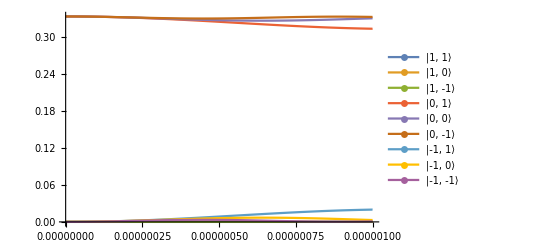

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
Plot[funcs, {t, tStart,tEnd/5}, PlotRange->{Full, Full},  PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}]]
```

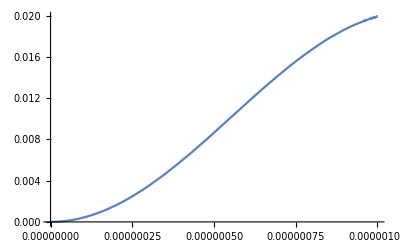

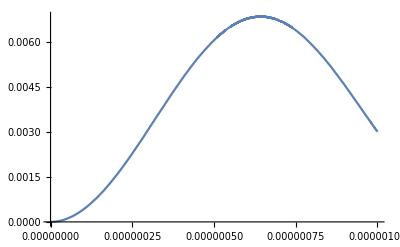

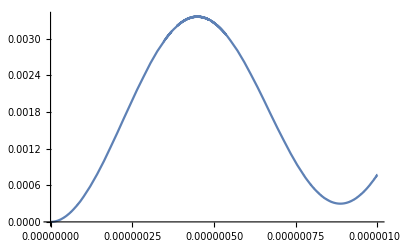

```mathematica
Plot[funcs[[7]], {t, tStart, tEnd/5}]
Plot[funcs[[8]], {t, tStart, tEnd/5}]
Plot[funcs[[9]], {t, tStart, tEnd/5}]
```

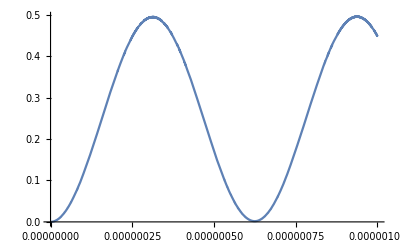
```mathematica
-Graphics-1
```

-Graphics-

```mathematica
v
```

v

```mathematica
3.1431151730484695*^9 +4.980766242049094*^6
```

3.1481×10^9

### Run simulation

```mathematica
stateVecs = IdentityMatrix[9];
simData = RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,spins,stateVecs,density0];
totalSimulationTime = simData["totalSimulationTime"];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.58907×10^-7}. NIntegrate obtained 2.8963×10^-12+0. ⅈ and 1.4969×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.20109×10^-6}. NIntegrate obtained 5.12655×10^-12+4.91185×10^-28 ⅈ and 1.40195×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.40617×10^-6}. NIntegrate obtained 5.16507×10^-12+0. ⅈ and 1.30611×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Total time taken (min) = 66.6714

### Results

#### Full simulation results

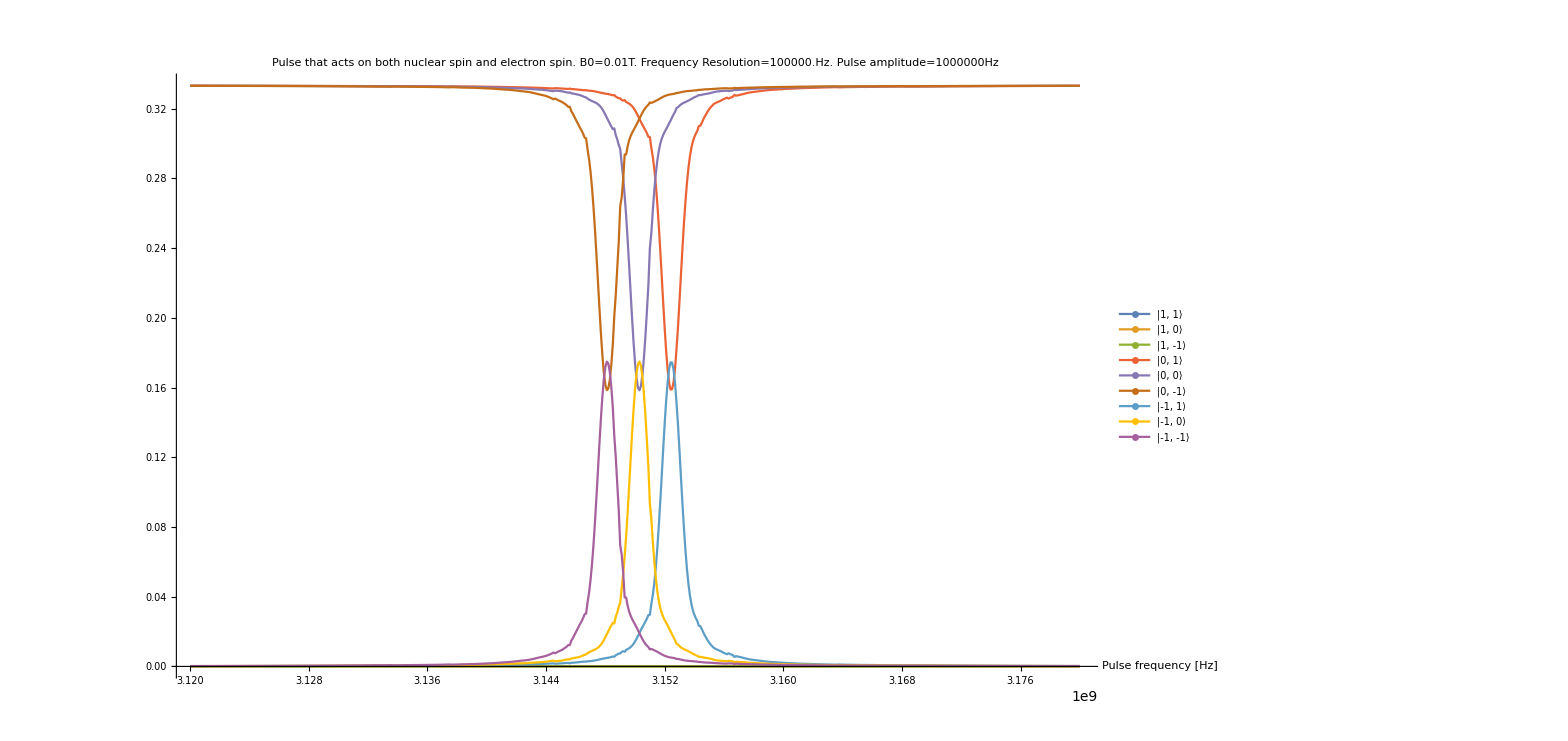

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
fullplot = ListPlot[simData["allstates"], PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full},Joined-> True, ImageSize -> 1200 ]
```

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
plotRange = {Full, Full};
GraphicsRow[{
ListPlot[simData["allstates"][[1;;3]], PlotLegends ->LineLegend[fullPlotlegend[[1;;3]], LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> plotRange,Joined-> False, ImageSize -> 420 ],
ListPlot[simData["allstates"][[4;;6]], PlotLegends ->LineLegend[fullPlotlegend[[4;;6]], LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> plotRange,Joined-> False, ImageSize -> 420 ],
ListPlot[simData["allstates"][[7;;9]], PlotLegends ->LineLegend[fullPlotlegend[[7;;9]], LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> plotRange,Joined-> False, ImageSize -> 420 ]
}, ImageSize->Full]
```

-Graphics-

#### ESR Plot

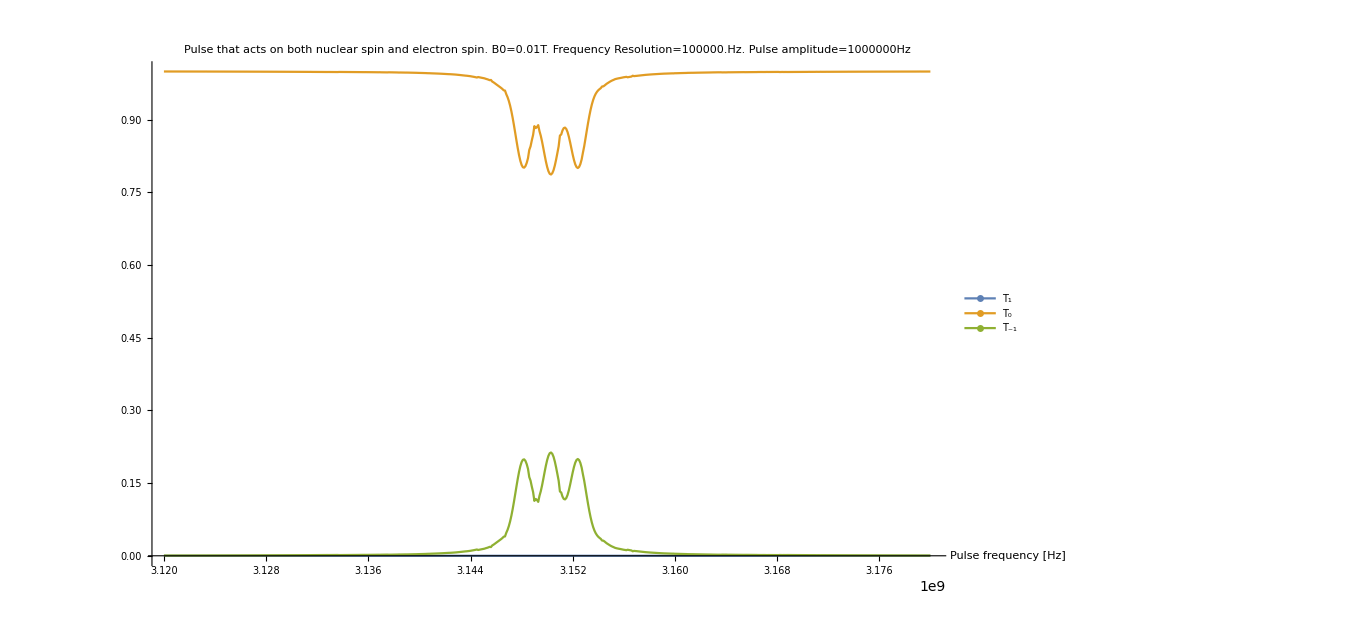

```mathematica
esrPlotlegend = {"T_1", "T_0", "T_-1"};
esrplot = ListPlot[{simData["T(1)"], simData["T(0)"], simData["T(-1)"]}, PlotLegends ->LineLegend[esrPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full}, ImageSize -> 1000 , Joined->True]
```

#### Angular momentum plot

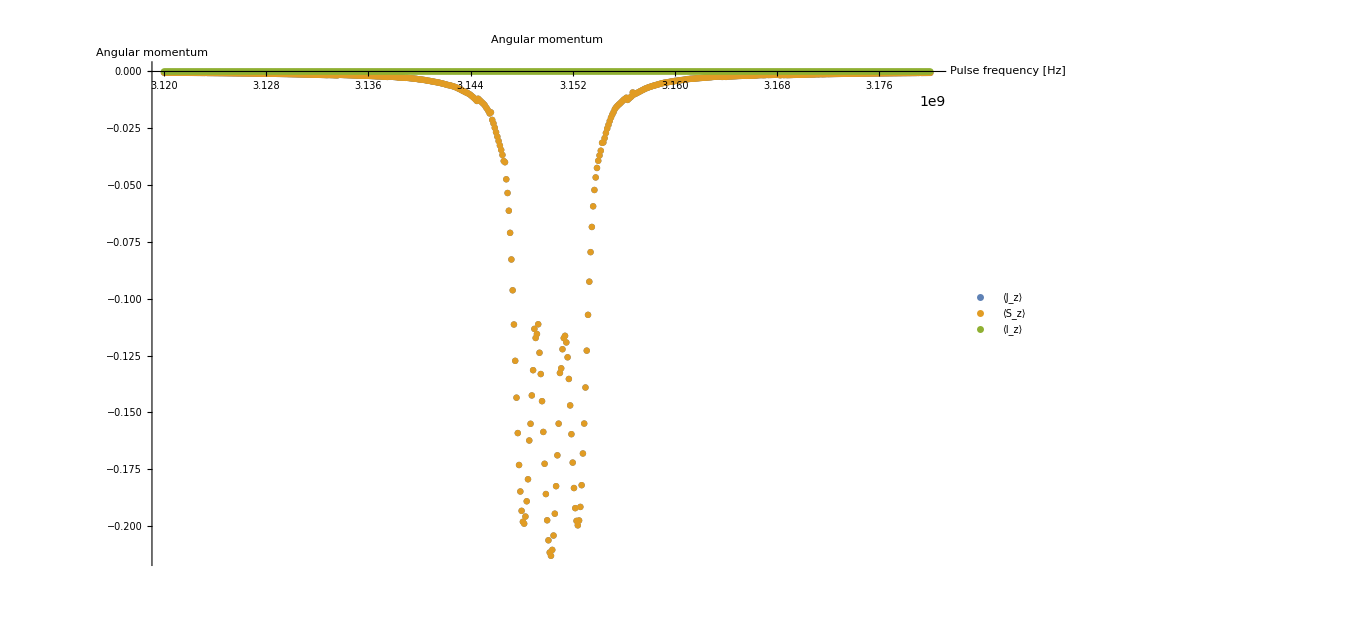

```mathematica
plotlegend = {"⟨J_z⟩", "⟨S_z⟩", "⟨I_z⟩"};
angmomplot = ListPlot[{simData["Jz"], simData["Sz"], simData["Iz"]}, PlotLegends ->LineLegend[plotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style["Angular momentum", 12], AxesLabel -> { "Pulse frequency [Hz]", "Angular momentum"}, PlotRange->{Full, Full}, ImageSize -> 1000, Joined->False ]
```

### Save simulation data

```mathematica
CreateDirectory["./" <> resultsFolder <> fileNamePrefix];
fpre =  "./" <> resultsFolder <> fileNamePrefix <> "/" <> fileNamePrefix;

Export[fpre<> "_data_T(1).csv",simData["T(1)"] ];
Export[fpre<> "_data_T(0).csv",simData["T(0)"]  ];
Export[fpre<> "_data_T(-1).csv",simData["T(-1)"]  ];

(* Save the ESR data *)
Do[
stateStr = "state(" <> ToString[i] <> "," <> ToString[j] <>")";
Export[fpre<>"_data_"<> stateStr <> ".csv",simData[i, j] ];
,{i, 1,-1, -1}, {j, 1, -1,-1}]

Export[fpre<> "_data_Jz.csv", simData["Jz"] ];
Export[fpre<> "_data_Sz.csv", simData["Sz"]];
Export[fpre<> "_data_Iz.csv", simData["Iz"]];
Export[fpre<> "_spectrum.csv", hamiltonianSpectrum];
Export[fpre<> "_ESRplot.pdf", esrplot];
Export[fpre<> "_fullplot.pdf", fullplot];
Export[fpre<> "_angmom_plot.pdf", angmomplot];
Save[ fpre <> "_params.wl", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```